## Fig. S8B

Plot effective number of species for as a function of tau_D, averaged over many random communities in the lattice model.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarLogPlots`"];
```

### get color scheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### define M function

```mathematica
effectiveSpecies[n_]:=
Module[{},
relN=n/Total[n];
modN=relN/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total;
mEff=E^entropy
]
```

### import and process data

```mathematica
geometrySet={"linear_noOligo","square_noOligo","hexagonal_noOligo"};
```

```mathematica
mSets=ConstantArray[0,Length[geometrySet]];
```

```mathematica
For[i=1,i≤Length[geometrySet],i++,

geometry=geometrySet[[i]];

params=Import["data\\lDiversity_s1pt4_"<>geometry<>"_epsilonSet.mx"];


If[i==1,epsilon=Table[(params[[j,1]]*16)/params[[j,2]],{j,9}];,epsilon=Table[(params[[j,1]])/params[[j,2]],{j,9}];];

numConditions=Length[epsilon];
allStrats=Import["data\\lDiversity_s1pt4_"<>geometry<>"_strats.mx"];
allFP=Import["data\\lDiversity_s1pt4_"<>geometry<>"_allFP.mx"];
lengths=Length/@allFP;
validFPIndices=Position[lengths,x_/;x==9];
(*delete cases that failed*)
validFP=allFP[[validFPIndices//Flatten]];

validStrats=allStrats[[validFPIndices//Flatten]];


theseEffectiveSpecies=Table[effectiveSpecies[validFP[[i,j]]],{i,Length[validFP]},{j,Length[params]}];

transposedSpecies=theseEffectiveSpecies//Transpose;
meanEffSpeciesChanges=Mean/@transposedSpecies;
stdEffSpeciesChanges=StandardDeviation/@transposedSpecies;
effOrderedPairs=Transpose[{epsilon,meanEffSpeciesChanges}];
effOorderedPairsError=Table[{effOrderedPairs[[i]],ErrorBar[stdEffSpeciesChanges[[i]]]},{i,Length[params]}];


mSets[[i]]=effOorderedPairsError;

]
```

```mathematica
mPlots={0,0,0};
```

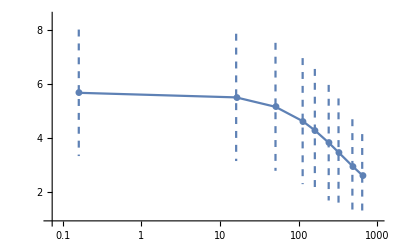

```mathematica
latticeIndex=1;
mPlots[[latticeIndex]]=ErrorListLogLinearPlot[mSets[[latticeIndex]],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[0,9,1]},PlotRange->{{.07,1000},{.9,8.5}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Dashed,l}&)]
```

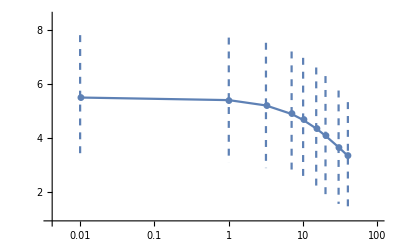

```mathematica
latticeIndex=2;
mPlots[[latticeIndex]]=ErrorListLogLinearPlot[mSets[[latticeIndex]],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.001,.01,.1,1,10,100,1000,10000},Range[0,9,1]},PlotRange->{{.004,100},{.9,8.5}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Dashed,l}&)]
```

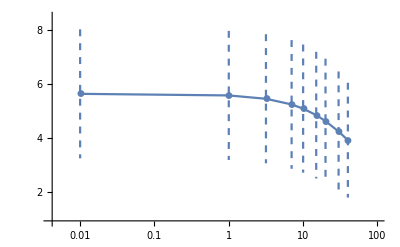

```mathematica
latticeIndex=3;
mPlots[[latticeIndex]]=ErrorListLogLinearPlot[mSets[[latticeIndex]],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.001,.01,.1,1,10,100,1000,10000},Range[0,9,1]},PlotRange->{{.004,100},{.9,8.5}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Dashed,l}&)]
```

```mathematica
Export["figS8B_left_1D.svg",mPlots[[1]]];
Export["figS8B_center_square.svg",mPlots[[2]]];
Export["figS8B_right_hexagonal.svg",mPlots[[3]]];
```